```mathematica
a0=1;
```

```mathematica
u0[x_]:=(0.09410609856839058)^(-1)*If[Abs[x]≤1/Sqrt[2],Exp[-1/(1/2-x^2)],0];
```

```mathematica
u0[x_]:=Cos[Pi x/3a0]
```

```mathematica
NIntegrate[u0[x],{x,-1,1}]
```

1.

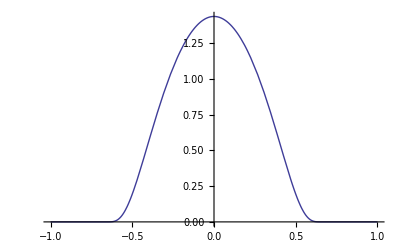

```mathematica
Plot[u0[x],{x,-1,1},AxesOrigin->{0,0}]
```

```mathematica
tmax=20;
```

```mathematica
(* an old pde we thought was right
sol=NDSolve[{D[u[x,t],t]==1/2D[u[x,t],{x,2}],u[x,0]==u0[x],u^(0,1)[a0,t]==-1/2u^(1,0)[a0,t],u^(0,1)[-a0,t]==1/2u^(1,0)[-a0,t]},u,{x,-a0,a0},{t,0,tmax}];*)
```

```mathematica
sol=NDSolve[{D[u[x,t],t]==1/2D[u[x,t],{x,2}],u[x,0]==u0[x],u[a0,t]==0,u[-a0,t]==0},u,{x,-a0,a0},{t,0,tmax}];
```

```mathematica
t0=0.1;t1=10;n=5;
```

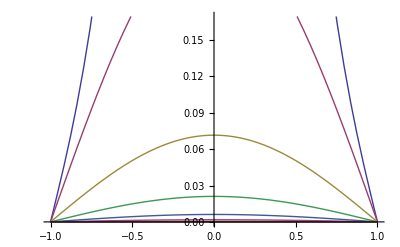

```mathematica
Plot[Evaluate[Table[Evaluate[u[x,t]/.sol]/.t->i,{i,t0,t1,(t1-t0)/n}]],{x,-1,1},ColorFunction->Automatic, AxesOrigin->{0,0}]
```

Find u_x, takes too long to plot

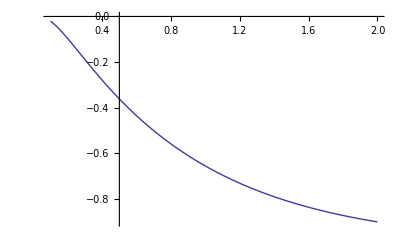

```mathematica
Plot[NIntegrate[Evaluate[D[First[u[x,t]/.sol],x]/.x->1],{t,0,s}],{s,0.1,2}]
```

```mathematica
s=%
```

Just find the value, should be first eigenvalue

```mathematica
NIntegrate[Evaluate[D[First[u[x,t]/.sol],x]/.x->1],{t,0,}]
```

-0.654923